# Chapter 4

## A: case qQ<M<0 (q=-3)

E1 topological charge

{4.2902,10.6808}

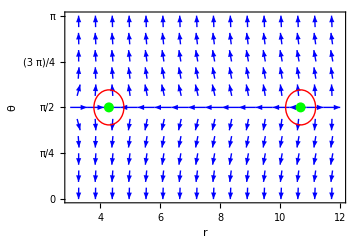

{0.930864,0.888866}

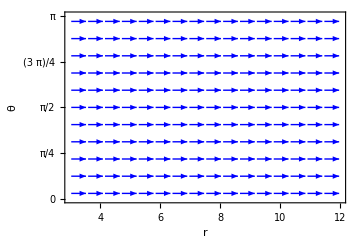

```mathematica
ClearAll["Global`*"]
rh=M+√(M^2-Q^2);
{rco->6.159297658513554};
{Eco->0.8534554427981478,Lco->5.897694740434756};
M=1;Q=0.6;q=-3;LL=6.5;
$Assumptions={r>0,0<= θ<= π,M>0};
ϕr=(r^2 (Q^2-M r) Cot[θ]^2+(r^2 (-Q^2+M r)-2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2+r (-Q^2 r+M r^2-√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
ϕθ=-(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={ϕr/(√(ϕr^2+ϕθ^2)),ϕθ/(√(ϕr^2+ϕθ^2))};
rls=r/.NSolve[0==ϕr/.θ->π/2,r,Reals]//Flatten
ran={3,12};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,Epilog->{Red,Thick,Circle[{rls[[1]],π/2},{0.5,0.3}],Circle[{rls[[2]],π/2},{0.5,0.3}],PointSize[0.02],Green,Point[{rls[[1]],π/2}],Point[{rls[[2]],π/2}]},FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
f=1-(2 M)/r+Q^2/r^2;θ=π/2;
E1=(q Q)/r+(√f √(2 LL^2 Csc[θ]^2+r^2 Csc[θ]^2-r^2 Cos[2 θ] Csc[θ]^2))/(√2 r)/.r->{rls[[1]],rls[[2]]}
Clear[LL]
LL=5.5;
ϕr=(r^2 (Q^2-M r) Cot[θ]^2+(r^2 (-Q^2+M r)-2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2+r (-Q^2 r+M r^2-√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
ϕθ=-(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={ϕr/(√(ϕr^2+ϕθ^2)),ϕθ/(√(ϕr^2+ϕθ^2))};
rls=r/.NSolve[0==ϕr/.θ->π/2,r,Reals];
ran={3,12};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

E2 topological charge

{rh→1.8,rL→2.34853,rs→2.37668,rp→2.73693}

{tco→2.35455}

{2.35,2.36}

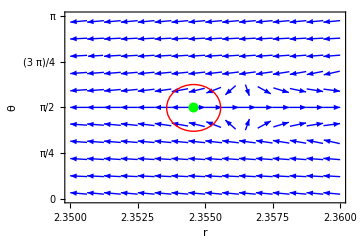

```mathematica
ClearAll["Global`*"]
M=1;Q=0.6;q=-3;LL=2.2;
rh=M+√(M^2-Q^2);
rP=1/2(3M+√(9 M^2-8 Q^2));
rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);
rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}

$Assumptions={r>0,0<= θ<= π,M>0};
vr2=(r^2 (-Q^2+M r) Cot[θ]^2+(r^2 (Q^2-M r)+2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2-r (-Q^2 r+M r^2+√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
vth2=(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={vr2/(√(vr2^2+vth2^2)),vth2/(√(vr2^2+vth2^2))};
(* the position of TCO can be solved from the vr2=0*)
tco=r/.NSolve[0==vr2/.θ->π/2,r,PositiveReals]//Flatten;
{"tco"->tco[[1]]}
ran={2.35,2.36}
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,Epilog->{Red,Thick,Circle[{tco[[1]],π/2},{0.001,0.4}],PointSize[0.02],Green,Point[{tco[[1]],π/2}]},FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
M=1;Q=0.6;q=-3;
rh=M+√(M^2-Q^2);
f[r]=1-(2M)/r+Q^2/r^2;
f'[r]=D[f[r],r];
{Et1,Lt1,Et2,Lt2} =ToExpression[Import["expression/EtLt.txt"]];
NSolve[D[Lt1,r]==0,r];
Select[%,#[[1,2]]∈Reals&&#[[1,2]]>rh&]//Flatten;
Ris=r/.%;
{"risco1"->%,"Et1"->Et1,"Lt1"->Lt1}/.r->Ris//Chop
```

{risco1→6.1593,Et1→0.853455,Lt1→5.89769}

{6.1593,0.853455,5.89769}

{rh→1.8,rL→2.34853,rs→2.37668,rp→2.73693}

{-8,15}

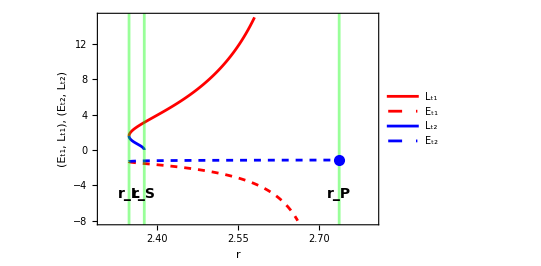

{-3,15}

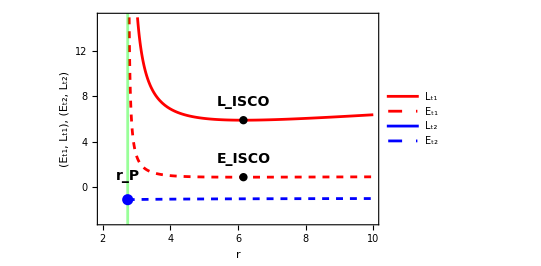

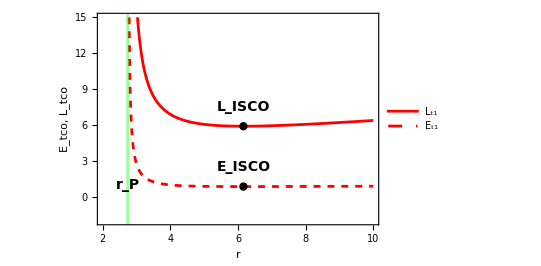

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
M=1;Q=0.6;q=-3;
{ris,Eis,Lis}={6.159297658513554,0.8534554427981478,5.897694740434756}
f[r]=1-(2M)/r+Q^2/r^2;
f'[r]=D[f[r],r];
{Et1,Lt1,Et2,Lt2} =ToExpression[Import["expression/EtLt.txt"]];
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));
rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
{Je2,Jl2}={Et2,Lt2}/.r->rP-10^-4;
(* note that Jl2 is imaginary*)

ran1={2.3,2.8};ran2={-8,15}
fig1=Plot[{Lt1,Et1,Lt2,Et2},{r,rL,rP},PlotRange->{ran1,ran2},PlotPoints->100,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["(E_t1, L_t1),  (E_t2, L_t2)",18,Italic]},AspectRatio->2/3,
PlotLegends->Placed[LineLegend[{Style["L_t1",14],Style["E_t1",14],Style["L_t2",14],Style["E_t2",14]},LegendLayout->{"Column",1}],{0.7,0.7}],GridLines->{{{rL,Directive[Green,Thickness[0.005]] },{rP,Directive[Green,Thickness[0.005]]},{rS,Directive[Green,Thickness[0.005]]}}, {}},Epilog->{Text[Style["r_L",14,Black,Bold],{rL,-5}],Text[Style["r_P",14,Black,Bold],{rP,-5}],Text[Style["r_S",14,Black,Bold],{rS,-5}],Blue,Thick,PointSize[0.02],Point[{rP,Je2}]}]

ran1={2,10};ran2={-3,15}
fig2=Plot[{Lt1,Et1,Lt2,Et2},{r,rP,10},PlotRange->{ran1,ran2},PlotPoints->100,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["(E_t1, L_t1),  (E_t2, L_t2)",18,Italic]},AspectRatio->2/3,PlotLegends->Placed[LineLegend[{Style["L_t1",14],Style["E_t1",14],Style["L_t2",14],Style["E_t2",14]},LegendLayout->{"Column",1}],{0.8,0.75}],GridLines->{{(*{rL,Directive[Green,Thickness[0.005]], }*){rP,Directive[Green,Thickness[0.005]]}(*,{rS,Directive[Green,Thickness[0.005]]}*)}, {}},Epilog->{ (*Text[Style["r_L",14,Black,Bold],{rL,-3}],*) Text[Style["r_P",14,Black,Bold],{rP,1}],Text[Style["L_ISCO",14,Black,Bold],{ris,7.5}],Text[Style["E_ISCO",14,Black,Bold],{ris,2.5}],Black,PointSize[0.015],Point[{ris,Eis}],Point[{ris,Lis}],Blue,Thick,PointSize[0.02],Point[{rP,Je2}]}]
(* We can find there is ISCO to Et1 *)

(* Here we focus on positive energy part. *)
fig3=Plot[{Et1,Lt1},{r,rP,10},PlotRange->{{2,10},{-2,15}},Frame->True,PlotPoints->100,PlotStyle->{{Red,Dashed},Red},LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["E_tco, L_tco",18,Italic]},AspectRatio->2/3,PlotLegends->Placed[LineLegend[{Style["E_t1",14],Style["L_t1",14]},LegendLayout->{"ReversedRow",2}],{0.8,0.8}],GridLines->{{{rP,Directive[Green,Thickness[0.005]] }}, {}},Epilog->{Text[Style["r_P",14,Black,Bold],{rP,1}],Text[Style["L_ISCO",14,Black,Bold],{ris,7.5}],Text[Style["E_ISCO",14,Black,Bold],{ris,2.5}],Black,PointSize[0.015],Point[{ris,Eis}],Point[{ris,Lis}]}]
```

```mathematica
Exit
```

## B Case -M<qQ<0 (q=-0.5)

E1 topological charge

{4.9549,6.18767}

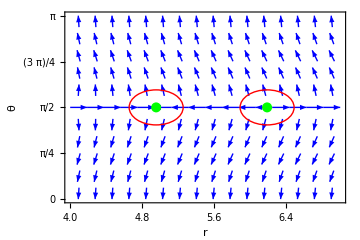

r

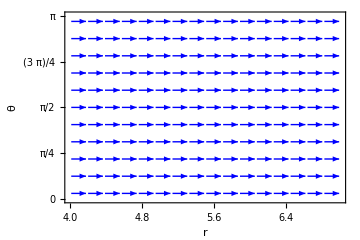

```mathematica
ClearAll["Global`*"]
rh=M+√(M^2-Q^2);
{rc0->5.502127841061523};
{Ec0->0.92044781065245,Lc0->3.75612212621818};
M=1;Q=0.6;q=-0.5;LL=3.78;
$Assumptions={r>0,0<= θ<= π,M>0};
ϕr=(r^2 (Q^2-M r) Cot[θ]^2+(r^2 (-Q^2+M r)-2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2+r (-Q^2 r+M r^2-√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
ϕθ=-(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={ϕr/(√(ϕr^2+ϕθ^2)),ϕθ/(√(ϕr^2+ϕθ^2))};
rls=r/.NSolve[0==ϕr/.θ->π/2,r,Reals]//Flatten
ran={4,7};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,Epilog->{Red,Thick,Circle[{rls[[1]],π/2},{0.3,0.3}],Circle[{rls[[2]],π/2},{0.3,0.3}],PointSize[0.02],Green,Point[{rls[[1]],π/2}],Point[{rls[[2]],π/2}]},FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
f=1-(2 M)/r+Q^2/r^2;θ=π/2;
E1=(q Q)/r+(√f √(2 LL^2 Csc[θ]^2+r^2 Csc[θ]^2-r^2 Cos[2 θ] Csc[θ]^2))/(√2 r)/.r->{rls[[1]],rls[[2]]};

(* L<Lisco *)
LL=3.73;
ϕr=(r^2 (Q^2-M r) Cot[θ]^2+(r^2 (-Q^2+M r)-2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2+r (-Q^2 r+M r^2-√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
ϕθ=-(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={ϕr/(√(ϕr^2+ϕθ^2)),ϕθ/(√(ϕr^2+ϕθ^2))};
rls=r/.NSolve[0==ϕr/.θ->π/2,r,Reals]
ran={4,7};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

E2 topological charge

{rh→1.8,rL→2.7278,rs→0.296703-0.137041 ⅈ,rp→2.73693}

{5.35748-0.530112 ⅈ,5.35748+0.530112 ⅈ}

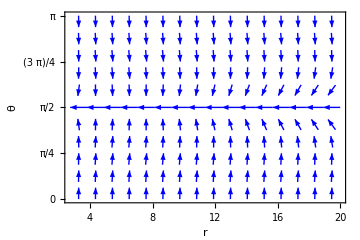

```mathematica
ClearAll["Global`*"]
{Lis,ris}={2.7631795998466875,5.409404205987615};
M=1;Q=0.6;q=-0.5;LL=2.75;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);
rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
vr2=(r^2 (-Q^2+M r) Cot[θ]^2+(r^2 (Q^2-M r)+2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2-r (-Q^2 r+M r^2+√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
vth2=(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={vr2/(√(vr2^2+vth2^2)),vth2/(√(vr2^2+vth2^2))};
(* the position of TCO can be solved from the vr2=0*)
tco=r/.NSolve[0==vr2/.θ->π/2,r]
(* At this point, there are not solution for TCO. *)
ran={rL,20};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

{rh→1.8,rL→2.7278,rs→0.296703-0.137041 ⅈ,rp→2.73693}

{4.869,6.08306}

{0,0}

-0.7/r^2+O[1/r]^3

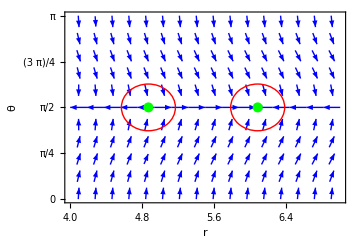

```mathematica
ClearAll["Global`*"]
{Lis,ris}={2.7631795998466875,5.409404205987615};
M=1;Q=0.6;q=-0.5;LL=2.78;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);
rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
vr2=(r^2 (-Q^2+M r) Cot[θ]^2+(r^2 (Q^2-M r)+2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2-r (-Q^2 r+M r^2+√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
vth2=(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={vr2/(√(vr2^2+vth2^2)),vth2/(√(vr2^2+vth2^2))};
(* the position of TCO can be solved from the vr2=0*)
tco=r/.NSolve[0==vr2/.θ->π/2,r]//Sort
vr2/.θ->π/2/.r->%//Chop
Plot[vr2/.θ->π/2,{r,1,100},PlotRange->{-10^-3,10^-3}];
(* This diagram tell us that there are 2 zeros, but from Nsolve calculation we got the 3 zeors, so that is no true.  *)
Series[vr2/.θ->π/2,{r,∞,2}]
ran={4,7};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,Epilog->{Red,Thick,Circle[{tco[[1]],π/2},{0.3,0.4}],Circle[{tco[[2]],π/2},{0.3,0.4}],PointSize[0.02],Green,Point[{tco[[1]],π/2}],Point[{tco[[2]],π/2}]},FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

decide the ISCO for Lt1 and Lt2

```mathematica
Exit
```

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
M=1;Q=0.6;q=-0.5;
rh=M+√(M^2-Q^2);
f[r]=1-(2M)/r+Q^2/r^2;
f'[r]=D[f[r],r];
{Et1,Lt1,Et2,Lt2} =ToExpression[Import["expression/EtLt.txt"]];
(* We can find there is ISCO to Lt1 *)
NSolve[D[Lt1,r]==0,r];
Select[%,#[[1,2]]∈Reals&&#[[1,2]]>rh&]//Flatten;
Ris=r/.%;
{"risco"->%,"Et1"->Et1,"Lt1"->Lt1}/.r->Ris//Chop
(* ISCO w.r.t Lt2*)
NSolve[D[Lt2,r]==0,r];
Select[%,#[[1,2]]∈Reals&&#[[1,2]]>rh&]//Flatten;
Ris=r/.%;
{"risco"->%,"Et1"->Et2,"Lt1"->Lt2}/.r->Ris//Chop
```

{risco→5.50213,Et1→0.920448,Lt1→3.75612}

{risco→5.4094,Et1→-0.955593,Lt1→2.76318}

{rh→1.8,rL→2.7278,rs→0.296703-0.137041 ⅈ,rp→2.73693}

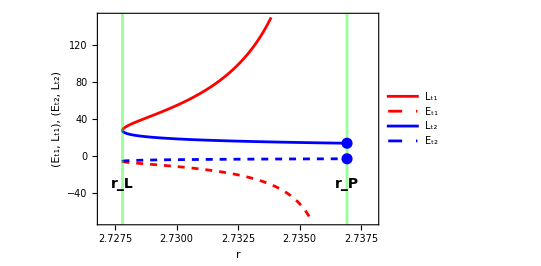

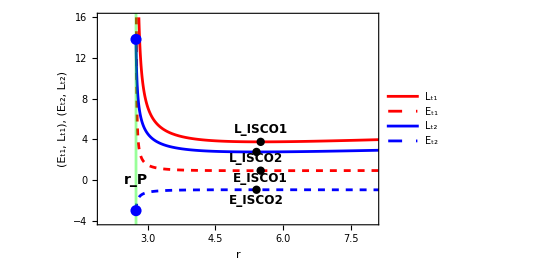

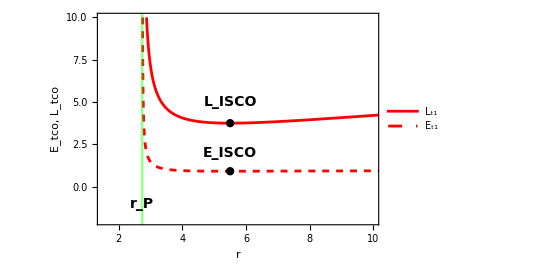

```mathematica
ClearAll["Global`*"]
M=1;Q=0.6;q=-0.5;
{Ris1,Eis1,Lis1}={5.502127841063909,0.9204478106524498,3.7561221262181803};
{Ris2,Eis2,Lis2}={5.409404205987615,-0.9555933762442997,2.7631795998466875};
f[r]=1-(2M)/r+Q^2/r^2;
f'[r]=D[f[r],r];
SetDirectory[NotebookDirectory[]];
{Et1,Lt1,Et2,Lt2} =ToExpression[Import["expression/EtLt.txt"]];
{Je2,Jl2}={Et2,Lt2}/.r->rP-10^-4;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));
rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
ran1={2.727,2.738};ran2={-70,150};

fig1=Plot[{Lt1,Et1,Lt2,Et2},{r,rL,rP},PlotRange->{ran1,ran2},PlotPoints->100,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["(E_t1, L_t1),  (E_t2, L_t2)",18,Italic]},AspectRatio->2/3,PlotLegends->Placed[LineLegend[{Style["L_t1",14],Style["E_t1",14],Style["L_t2",14],Style["E_t2",14]},LegendLayout->{"Column",1}],{0.75,0.7}],GridLines->{{{rL,Directive[Green,Thickness[0.005]] },{rP,Directive[Green,Thickness[0.005]]}(*,{rS,Directive[Green,Thickness[0.005]]}*)}, {}},Epilog->{Text[Style["r_L",14,Black,Bold],{rL,-30}],Text[Style["r_P",14,Black,Bold],{rP,-30}],Blue,Thick,PointSize[0.02],Point[{rP,Je2}],Point[{rP,Jl2}](*,Circle[{rP,Je2},{0.0001,4}]*)}]


(* Here we need the zoom in figure for the interveal [rL,rP]. *)

ran1={2,8};ran2={-4,16};
fig2=Plot[{Lt1,Et1,Lt2,Et2},{r,rP,10},PlotRange->{ran1,ran2},PlotPoints->100,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,Axes->None,FrameLabel->{Style["r",18,Italic],Style["(E_t1, L_t1),  (E_t2, L_t2)",18,Italic]},AspectRatio->2/3,GridLines->{{ {rP,Directive[Green,Thickness[0.005]]} }, {}},
PlotLegends->Placed[LineLegend[{Style["L_t1",14],Style["E_t1",14],Style["L_t2",14],Style["E_t2",14]},LegendLayout->{"Column",1}],{0.75,0.7}],Epilog->{  Text[Style["r_P",14,Black,Bold],{rP,0}] ,Blue,Thick,PointSize[0.02],Point[{rP,Je2}],Point[{rP,Jl2}],Text[Style["L_ISCO1",12,Black,Bold],{Ris1,5}],Text[Style["E_ISCO1",12,Black,Bold],{Ris1,0.2}],Text[Style["L_ISCO2",12,Black,Bold],{Ris2,2.1}],Text[Style["E_ISCO2",12,Black,Bold],{Ris2,-2}],Black,PointSize[0.015],Point[{Ris1,Eis1}],Point[{Ris1,Lis1}],Point[{Ris2,Eis2}],Point[{Ris2,Lis2}]}(*,ScalingFunctions->{"Log10"}*)]


(* Here we focus on positive energy part. *)
Plot[{Et1,Lt1},{r,rP,20},PlotRange->{{1.5,10},{-2,10}},Frame->True,PlotPoints->100,PlotStyle->{{Red,Dashed},Red},LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["E_tco, L_tco",18,Italic]},AspectRatio->2/3,PlotLegends->Placed[LineLegend[{Style["E_t1",14],Style["L_t1",14]},LegendLayout->{"ReversedRow",2}],{0.7,0.8}],GridLines->{{{rP,Directive[Green,Thickness[0.005]] }}, {}},Epilog->{Text[Style["r_P",14,Black,Bold],{rP,-1}],Text[Style["L_ISCO",14,Black,Bold],{Ris1,5}],Text[Style["E_ISCO",14,Black,Bold],{Ris1,2}],Black,PointSize[0.015],Point[{Ris1,Eis1}],Point[{Ris1,Lis1}]}]
```

## C case 0<qQ<M (q=1.2)

E1 topological charge

{4.85493,7.38822}

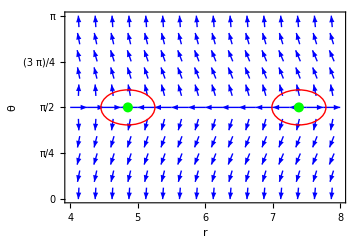

{0.985353,0.984671}

r

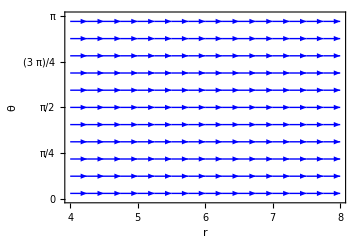

```mathematica
ClearAll["Global`*"]
rh=M+√(M^2-Q^2);
{r->5.887110087738307};{Esco->0.9835220101506544,Lsco->1.9160215133347906};
M=1;Q=0.6;q=1.2;LL=1.95;
$Assumptions={r>0,0<= θ<= π,M>0};
ϕr=(r^2 (Q^2-M r) Cot[θ]^2+(r^2 (-Q^2+M r)-2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2+r (-Q^2 r+M r^2-√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
ϕθ=-(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={ϕr/(√(ϕr^2+ϕθ^2)),ϕθ/(√(ϕr^2+ϕθ^2))};
ran={4,8};
rls=r/.NSolve[0==ϕr/.θ->π/2,r,Reals]//Flatten
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,Epilog->{Red,Thick,Circle[{rls[[1]],π/2},{0.4,0.3}],Circle[{rls[[2]],π/2},{0.4,0.3}],PointSize[0.02],Green,Point[{rls[[1]],π/2}],Point[{rls[[2]],π/2}]},FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
f=1-(2 M)/r+Q^2/r^2;θ=π/2;
E1=(q Q)/r+(√f √(2 LL^2 Csc[θ]^2+r^2 Csc[θ]^2-r^2 Cos[2 θ] Csc[θ]^2))/(√2 r)/.r->{rls[[1]],rls[[2]]}
(*  L>Lisco *)
Clear[LL]
LL=1.85;
ϕr=(r^2 (Q^2-M r) Cot[θ]^2+(r^2 (-Q^2+M r)-2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2+r (-Q^2 r+M r^2-√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
ϕθ=-(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={ϕr/(√(ϕr^2+ϕθ^2)),ϕθ/(√(ϕr^2+ϕθ^2))};
rls=r/.NSolve[0==ϕr/.θ->π/2,r,Reals]
ran={4,8};
VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

E2 topological charge

{rh→1.8,rL→2.68338,rs→-0.804911,rp→2.73693}

{58.8814,5.19662-1.55345 ⅈ,5.19662+1.55345 ⅈ,0.262841-0.00566949 ⅈ,0.262841+0.00566949 ⅈ}

{-0.000408249,1.03497×10^-16+5.80115×10^-16 ⅈ,1.03497×10^-16-5.80115×10^-16 ⅈ,4.98991×10^-12-2.58522×10^-11 ⅈ,4.98991×10^-12+2.58522×10^-11 ⅈ}

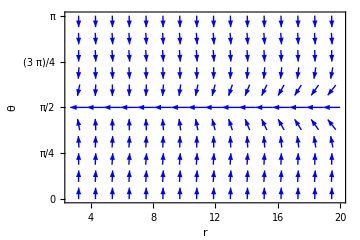

```mathematica
ClearAll["Global`*"]
{Lis,ris}={4.388168078105018,5.66533713502036};
M=1;Q=0.6;q=1.2;LL=4.2;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);
rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
vr2=(r^2 (-Q^2+M r) Cot[θ]^2+(r^2 (Q^2-M r)+2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2-r (-Q^2 r+M r^2+√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
vth2=(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={vr2/(√(vr2^2+vth2^2)),vth2/(√(vr2^2+vth2^2))};
(* the position of TCO can be solved from the vr2=0*)
tco=r/.NSolve[0==vr2/.θ->π/2,r]
vr2/.θ->π/2/.r->%
(* At this point, there are not solution for TCO. *)
ran={rL,20};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,(*Epilog->{Red,Thick,Circle[{tco[[1]],π/2},{0.001,0.4}],PointSize[0.02],Green,Point[{tco[[1]],π/2}]},*)FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

{rh→1.8,rL→2.68338,rs→-0.804911,rp→2.73693}

{4.64814,7.25918}

{0,0}

-1.72/r^2+O[1/r]^3

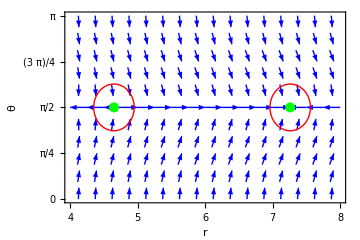

```mathematica
ClearAll["Global`*"]
{Lis,ris}={4.388168078105018,5.66533713502036};
M=1;Q=0.6;q=1.2;LL=4.5;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);
rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
vr2=(r^2 (-Q^2+M r) Cot[θ]^2+(r^2 (Q^2-M r)+2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2-r (-Q^2 r+M r^2+√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
vth2=(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={vr2/(√(vr2^2+vth2^2)),vth2/(√(vr2^2+vth2^2))};
(* the position of TCO can be solved from the vr2=0*)
tco=r/.NSolve[0==vr2/.θ->π/2,r,Reals]//Sort
vr2/.θ->π/2/.r->%//Chop
Plot[vr2/.θ->π/2,{r,1,100},PlotRange->{-10^-3,10^-3}];
(* This diagram tell us that there are 2 zeros, but from Nsolve calculation we got the 3 zeors, so that is no true.  *)
Series[vr2/.θ->π/2,{r,∞,2}]
ran={4,8};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,Epilog->{Red,Thick,Circle[{tco[[1]],π/2},{0.3,0.4}],Circle[{tco[[2]],π/2},{0.3,0.4}],PointSize[0.02],Green,Point[{tco[[1]],π/2}],Point[{tco[[2]],π/2}]},FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
M=1;Q=0.6;q=1.2;
rh=M+√(M^2-Q^2);
f[r]=1-(2M)/r+Q^2/r^2;
f'[r]=D[f[r],r];
{Et1,Lt1,Et2,Lt2} =ToExpression[Import["expression/EtLt.txt"]];
(* We can find there is ISCO to Lt1 *)
NSolve[D[Lt1,r]==0,r];
Select[%,#[[1,2]]∈Reals&&#[[1,2]]>rh&]//Flatten;
Ris=r/.%;
{"risco1"->%,"Et1"->Et1,"Lt1"->Lt1}/.r->Ris//Chop
(* ISCO w.r.t Lt2*)
NSolve[D[Lt2,r]==0,r];
Select[%,#[[1,2]]∈Reals&&#[[1,2]]>rh&]//Flatten;
Ris=r/.%;
{"risco2"->%,"Et1"->Et2,"Lt1"->Lt2}/.r->Ris//Chop
```

{risco1→5.88711,Et1→0.983522,Lt1→1.91602}

{risco2→5.66534,Et1→-0.899106,Lt1→4.38817}

{rh→1.8,rL→2.68338,rs→-0.804911,rp→2.73693}

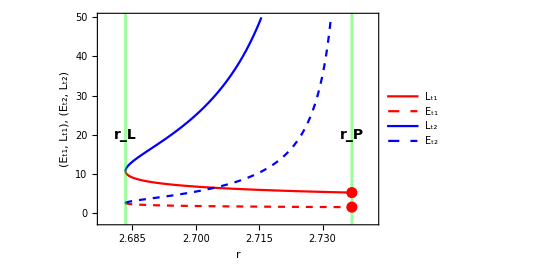

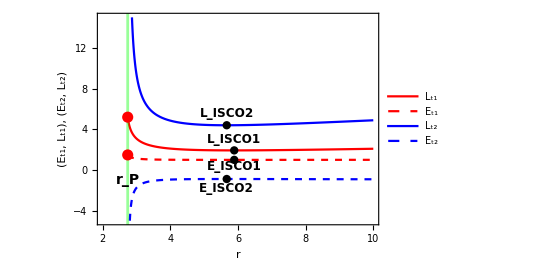

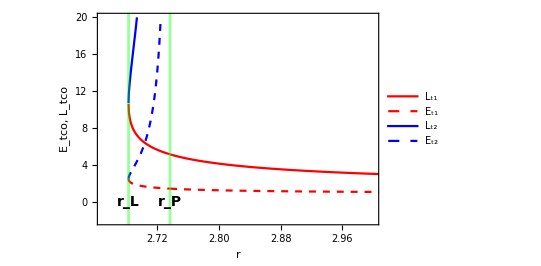

```mathematica
ClearAll["Global`*"]
M=1;Q=0.6;q=1.2;
{Ris1,Eis1,Lis1}={5.887110087730256,0.9835220101506545,1.9160215133347904};
{Ris2,Eis2,Lis2}={5.66533713502036,-0.8991056667104562,4.388168078105018};
f[r]=1-(2M)/r+Q^2/r^2;
f'[r]=D[f[r],r];
{Et1,Lt1,Et2,Lt2} =ToExpression[Import["expression/EtLt.txt"]];
{Je2,Jl2}={Et1,Lt1}/.r->rP-10^-4;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));
rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
ran1={2.678,2.742};ran2={-2,50};

fig1=Plot[{Lt1,Et1,Lt2,Et2},{r,rL,rP-10^-4},PlotRange->{ran1,ran2},PlotPoints->100,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["(E_t1, L_t1),  (E_t2, L_t2)",18,Italic]},AspectRatio->2/3,PlotLegends->Placed[LineLegend[{Style["L_t1",14],Style["E_t1",14],Style["L_t2",14],Style["E_t2",14]},LegendLayout->{"Column",1}],{0.23,0.78}],GridLines->{{{rL,Directive[Green,Thickness[0.005]] },{rP,Directive[Green,Thickness[0.005]]}(*,{rS,Directive[Green,Thickness[0.005]]}*)}, {}},Epilog->{Text[Style["r_L",14,Black,Bold],{rL,20}],Text[Style["r_P",14,Black,Bold],{rP,20}],Red,Thick,PointSize[0.02],Point[{rP,Je2}],Point[{rP,Jl2}](*,Circle[{rP,Je2},{0.0001,4}]*)}]


(* Here we need the zoom in figure for the interveal [rL,rP]. *)
ran1={2,10};ran2={-5,15};
fig2=Plot[{Lt1,Et1,Lt2,Et2},{r,rP,10},PlotRange->{ran1,ran2},PlotPoints->100,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["(E_t1, L_t1),  (E_t2, L_t2)",18,Italic]},AspectRatio->2/3,GridLines->{{ {rP,Directive[Green,Thickness[0.005]]} }, {}},
PlotLegends->Placed[LineLegend[{Style["L_t1",14],Style["E_t1",14],Style["L_t2",14],Style["E_t2",14]},LegendLayout->{"Column",1}],{0.8,0.75}],Epilog->{  Text[Style["r_P",14,Black,Bold],{rP,-1}] ,Red,Thick,PointSize[0.02],Point[{rP,Je2}],Point[{rP,Jl2}],Text[Style["L_ISCO1",12,Black,Bold],{Ris1,3}],Text[Style["E_ISCO1",12,Black,Bold],{Ris1,0.3}],Text[Style["L_ISCO2",12,Black,Bold],{Ris2,5.5}],Text[Style["E_ISCO2",12,Black,Bold],{Ris2,-1.8}],Black,PointSize[0.015],Point[{Ris1,Eis1}],Point[{Ris1,Lis1}],Point[{Ris2,Eis2}],Point[{Ris2,Lis2}]},Axes->False]


(* Here we focus on positive energy part. *)
(* completed TCO *)
figa=Plot[{Et2, Lt2},{r,2.4,rP},PlotRange->{{2.65,3.0},{-2,20}},Frame->True,PlotPoints->100,PlotStyle->{{Blue,Dashed},Blue},LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["E_tco, L_tco",18,Italic]},AspectRatio->2/3,GridLines->{{{rL,Directive[Green,Thickness[0.005]] },{rP,Directive[Green,Thickness[0.005]]}}, {}},Epilog->{Text[Style["r_L",14,Black,Bold],{rL,0}],Text[Style["r_P",14,Black,Bold],{rP,0}]}
];
figb=Plot[{Et1,Lt1},{r,2.4,3.8},PlotRange->{{2.5,3.8},{-3,15}},Frame->True,PlotPoints->100,PlotStyle->{{Red,Dashed},Red},LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["E_t1, L_t1",18,Italic]},AspectRatio->2/3,GridLines->{{{rL,Directive[Green,Thickness[0.005]] }}, {}}];
Show[figa,figb];
Legended[%,Placed[LineLegend[{Red,{Red,Dashed},Blue,{Blue,Dashed}},{Style["L_t1",14,Bold],Style["E_t1",14,Bold],Style["L_t2",14,Bold],Style["E_t2",14,Bold]},LegendLayout->{"Column",1}],{0.78,0.65}]]
(* Note that The curves Etco and Ltco have ISCO, but we not show them! *)
```

## D case: M<qQ

### 1 Subcase M<qQ<q_tQ (q=2.1)

E1 topological charge

{2.60092}

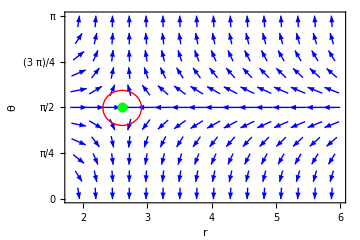

{2.60253}

```mathematica
ClearAll["Global`*"]
rh=M+√(M^2-Q^2);
M=1;Q=0.6;q=2.1;LL=10;
$Assumptions={r>0,0<= θ<= π,M>0};
ϕr=(r^2 (Q^2-M r) Cot[θ]^2+(r^2 (-Q^2+M r)-2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2+r (-Q^2 r+M r^2-√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
ϕθ=-(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={ϕr/(√(ϕr^2+ϕθ^2)),ϕθ/(√(ϕr^2+ϕθ^2))};
ran={rh,6};
rls=r/.NSolve[0==ϕr/.θ->π/2,r,PositiveReals]//Flatten
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,Epilog->{Red,Thick,Circle[{rls[[1]],π/2},{0.3,0.3}],PointSize[0.02],Green,Point[{rls[[1]],π/2}]},FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
f=1-(2 M)/r+Q^2/r^2;θ=π/2;
E1=(q Q)/r+(√f √(2 LL^2 Csc[θ]^2+r^2 Csc[θ]^2-r^2 Cos[2 θ] Csc[θ]^2))/(√2 r)/.r->rls
```

E2 topological charge

{rh→1.8,rL→2.56447,rs→3.98985,rp→2.73693}

{-100.959,5.88697-0.343254 ⅈ,5.88697+0.343254 ⅈ,0.262401-0.00804502 ⅈ,0.262401+0.00804502 ⅈ}

{0.000249675,0,0,0,0}

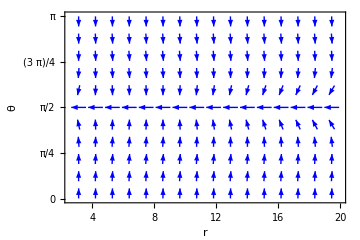

```mathematica
ClearAll["Global`*"]
{Lis,ris}={5.158729251967719,5.9067920331424535};
M=1;Q=0.6;q=2.1;LL=5.15;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);
rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
vr2=(r^2 (-Q^2+M r) Cot[θ]^2+(r^2 (Q^2-M r)+2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2-r (-Q^2 r+M r^2+√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
vth2=(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={vr2/(√(vr2^2+vth2^2)),vth2/(√(vr2^2+vth2^2))};
(* the position of TCO can be solved from the vr2=0*)
tco=r/.NSolve[0==vr2/.θ->π/2,r]
vr2/.θ->π/2/.r->%//Chop
(* At this point, there are not solution for TCO. *)
ran={rL,20};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,(*Epilog->{Red,Thick,Circle[{tco[[1]],π/2},{0.001,0.4}],PointSize[0.02],Green,Point[{tco[[1]],π/2}]},*)FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

{rh→1.8,rL→2.56447,rs→3.98985,rp→2.73693}

{5.24557,6.7564}

{0,0}

-2.26/r^2+O[1/r]^3

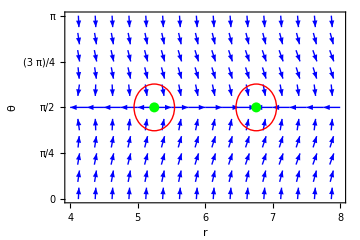

```mathematica
ClearAll["Global`*"]
{Lis,ris}={5.158729251967719,5.9067920331424535};
M=1;Q=0.6;q=2.1;LL=5.2;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);
rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
vr2=(r^2 (-Q^2+M r) Cot[θ]^2+(r^2 (Q^2-M r)+2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2-r (-Q^2 r+M r^2+√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
vth2=(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={vr2/(√(vr2^2+vth2^2)),vth2/(√(vr2^2+vth2^2))};
(* the position of TCO can be solved from the vr2=0*)
tco=r/.NSolve[0==vr2/.θ->π/2,r,Reals]//Sort
vr2/.θ->π/2/.r->%//Chop
Plot[vr2/.θ->π/2,{r,1,100},PlotRange->{-10^-3,10^-3}];
(* This diagram tell us that there are 2 zeros, but from Nsolve calculation we got the 3 zeors, so that is no true.  *)
Series[vr2/.θ->π/2,{r,∞,2}]
ran={4,8};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,Epilog->{Red,Thick,Circle[{tco[[1]],π/2},{0.3,0.4}],Circle[{tco[[2]],π/2},{0.3,0.4}],PointSize[0.02],Green,Point[{tco[[1]],π/2}],Point[{tco[[2]],π/2}]},FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
M=1;Q=0.6;q=2.1;
rh=M+√(M^2-Q^2);
f[r]=1-(2M)/r+Q^2/r^2;
f'[r]=D[f[r],r];
{Et1,Lt1,Et2,Lt2} =ToExpression[Import["expression/EtLt.txt"]];
(* We can find there is ISCO to Lt1 *)
(*NSolve[D[Lt1,r]==0,r];
Select[%,#[[1,2]]∈Reals&&#[[1,2]]>rh&]//Flatten;
Ris=r/.%;
{"risco1"->%,"Et1"->Et1,"Lt1"->Lt1}/.r->Ris//Chop
*)

(* ISCO w.r.t Lt2*)
NSolve[D[Lt2,r]==0,r];
Select[%,#[[1,2]]∈Reals&&#[[1,2]]>rh&]//Flatten;
Ris=r/.%;
{"risco2"->%,"Et1"->Et2,"Lt1"->Lt2}/.r->Ris//Chop
```

{risco2→5.90679,Et1→-0.874842,Lt1→5.15873}

{rh→1.8,rL→2.56447,rs→3.98985,rp→2.73693}

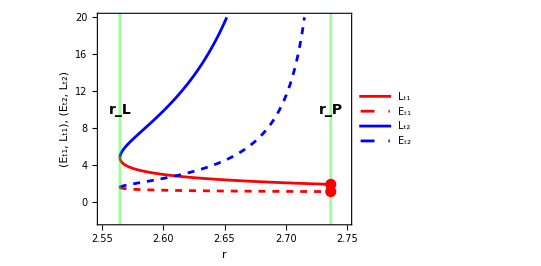

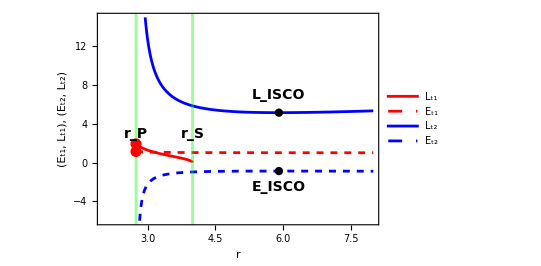

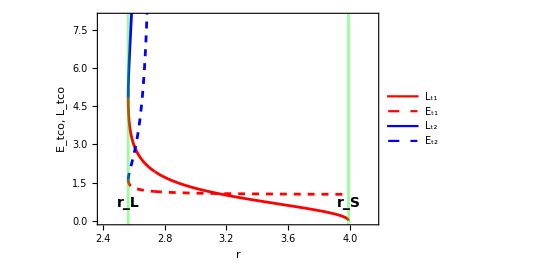

```mathematica
ClearAll["Global`*"]
M=1;Q=0.6;q=2.1;
(*{Ris1,Eis1,Lis1}={};*)
{Ris2,Eis2,Lis2}={5.9067920331424535,-0.8748419314185062,5.158729251967719};
f[r]=1-(2M)/r+Q^2/r^2;
f'[r]=D[f[r],r];
SetDirectory[NotebookDirectory[]];
{Et1,Lt1,Et2,Lt2} =ToExpression[Import["expression/EtLt.txt"]];
{Je2,Jl2}={Et1,Lt1}/.r->rP-10^-4;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));
rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
ran1={2.55,2.75};ran2={-2,20};

fig1=Plot[{Lt1,Et1,Lt2,Et2},{r,rL,rP-10^-4},PlotRange->{ran1,ran2},PlotPoints->100,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["(E_t1, L_t1),  (E_t2, L_t2)",18,Italic]},AspectRatio->2/3,PlotLegends->Placed[LineLegend[{Style["L_t1",14],Style["E_t1",14],Style["L_t2",14],Style["E_t2",14]},LegendLayout->{"Column",1}],{0.62,0.78}],GridLines->{{{rL,Directive[Green,Thickness[0.005]] },{rP,Directive[Green,Thickness[0.005]]},{rS,Directive[Green,Thickness[0.005]]}}, {}},Epilog->{Text[Style["r_L",14,Black,Bold],{rL,10}],Text[Style["r_P",14,Black,Bold],{rP,10}],Text[Style["r_S",14,Black,Bold],{rS,-5}],Red,Thick,PointSize[0.02],Point[{rP,Je2}],Point[{rP,Jl2}](*,Circle[{rP,Je2},{0.0001,4}]*)}]


(* Here we need the zoom in figure for the interveal [rL,rP]. *)
ran1={2,8};ran2={-6,15};
fig2=Plot[{Lt1,Et1,Lt2,Et2},{r,rP,8},PlotRange->{ran1,ran2},PlotPoints->100,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["(E_t1, L_t1),  (E_t2, L_t2)",18,Italic]},AspectRatio->2/3,GridLines->{{ {rP,Directive[Green,Thickness[0.005]]},{rS,Directive[Green,Thickness[0.005]]} }, {}},
PlotLegends->Placed[LineLegend[{Style["L_t1",14],Style["E_t1",14],Style["L_t2",14],Style["E_t2",14]},LegendLayout->{"Column",1}],{0.85,0.75}],Epilog->{  Text[Style["r_P",14,Black,Bold],{rP,3}],Text[Style["r_S",14,Black,Bold],{rS,3}] ,Red,Thick,PointSize[0.02],Point[{rP,Je2}],Point[{rP,Jl2}],Text[Style["L_ISCO",14,Black,Bold],{Ris2,7}],Text[Style["E_ISCO",14,Black,Bold],{Ris2,-2.5}],Black,PointSize[0.015],(*Point[{Ris1,Eis1}],Point[{Ris1,Lis1}],*) Point[{Ris2,Eis2}],Point[{Ris2,Lis2}]}]

(* Here we focus on positive energy part. *)
(* completed TCO *)
figa=Plot[{Et1,Lt1},{r,rL,rS},PlotRange->{{2.4,4.15},{0,8}},Frame->True,PlotPoints->100,PlotStyle->{{Red,Dashed},Red},LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["E_tco, L_tco",18,Italic]},AspectRatio->2/3,GridLines->{{{rL,Directive[Green,Thickness[0.005]] },{rS,Directive[Green,Thickness[0.005]]}}, {}},Epilog->{Text[Style["r_L",14,Black,Bold],{rL,0.7}],Text[Style["r_S",14,Black,Bold],{rS,0.7}]}
];

figb=Plot[{Et2,Lt2},{r,rL,rP},PlotRange->{{2.4,4.5},{0,20}},Frame->True,PlotPoints->100,PlotStyle->{{Blue,Dashed},Blue},LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["E_t2, L_t2",18,Italic]},AspectRatio->2/3,GridLines->{{{rL,Directive[Green,Thickness[0.005]] },{rP,Directive[Green,Thickness[0.005]]}}, {}}];
Show[figa,figb];
Legended[%,Placed[LineLegend[{Red,{Red,Dashed},Blue,{Blue,Dashed}},{Style["L_t1",14,Bold],Style["E_t1",14,Bold],Style["L_t2",14,Bold],Style["E_t2",14,Bold]},LegendLayout->{"Column",1}],{0.6,0.7}]]
```

### 2 Subcase: q_t Q<qQ<∞ (Q=3.8)

E1 topological charge

{2.23897}

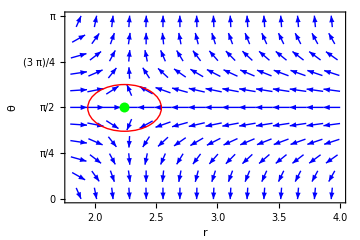

1.70976

```mathematica
ClearAll["Global`*"]
rh=M+√(M^2-Q^2);
M=1;Q=0.6;q=3.8;LL=2.9;
$Assumptions={r>0,0<= θ<= π,M>0};
ϕr=(r^2 (Q^2-M r) Cot[θ]^2+(r^2 (-Q^2+M r)-2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2+r (-Q^2 r+M r^2-√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
ϕθ=-(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={ϕr/(√(ϕr^2+ϕθ^2)),ϕθ/(√(ϕr^2+ϕθ^2))};
ran={rh,4};
rls=r/.NSolve[0==ϕr/.θ->π/2,r,PositiveReals]//Flatten
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,Epilog->{Red,Thick,Circle[{rls[[1]],π/2},{0.3,0.4}],PointSize[0.02],Green,Point[{rls[[1]],π/2}]},FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
f=1-(2 M)/r+Q^2/r^2;θ=π/2;
E1=(q Q)/r+(√f √(2 LL^2 Csc[θ]^2+r^2 Csc[θ]^2-r^2 Cos[2 θ] Csc[θ]^2))/(√2 r)/.r->rls[[1]]
```

E2 topological charge

{rh→1.8,rL→1.98,rs→2.10807,rp→2.73693}

{6.35404-0.454449 ⅈ,6.35404+0.454449 ⅈ,0.261577-0.0113822 ⅈ,0.261577+0.0113822 ⅈ}

{0,0,0,0}

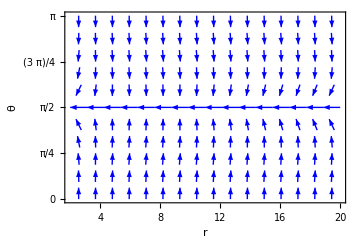

```mathematica
ClearAll["Global`*"]
{Lis,ris}={6.53564,6.384943395371074};
M=1;Q=0.6;q=3.8;LL=6.52;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);
rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
vr2=(r^2 (-Q^2+M r) Cot[θ]^2+(r^2 (Q^2-M r)+2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2-r (-Q^2 r+M r^2+√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
vth2=(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={vr2/(√(vr2^2+vth2^2)),vth2/(√(vr2^2+vth2^2))};
(* the position of TCO can be solved from the vr2=0*)
tco=r/.NSolve[0==vr2/.θ->π/2,r]
vr2/.θ->π/2/.r->%//Chop
(* At this point, there are not solution for TCO. *)
ran={rL,20};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,(*Epilog->{Red,Thick,Circle[{tco[[1]],π/2},{0.001,0.4}],PointSize[0.02],Green,Point[{tco[[1]],π/2}]},*)FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

{rh→1.8,rL→1.98,rs→2.10807,rp→2.73693}

{5.97556,6.85117}

{0,0}

-3.28/r^2+O[1/r]^3

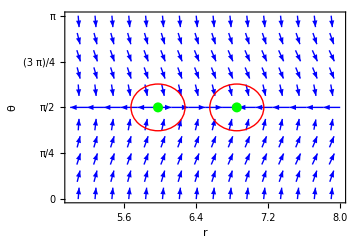

```mathematica
ClearAll["Global`*"]
{Lis,ris}={6.53564,6.384943395371074};
M=1;Q=0.6;q=3.8;LL=6.55;
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);
rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
vr2=(r^2 (-Q^2+M r) Cot[θ]^2+(r^2 (Q^2-M r)+2 LL^2 (2 Q^2-3 M r+r^2)) Csc[θ]^2-r (-Q^2 r+M r^2+√2 q Q √((Q^2+r (-2 M+r)) (2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)))/(√2 r^4 √((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2));
vth2=(√2 LL^2 Cot[θ] Csc[θ]^2)/(r^3 √(((2 LL^2+r^2-r^2 Cos[2 θ]) Csc[θ]^2)/(Q^2+r (-2 M+r))));
nvec={vr2/(√(vr2^2+vth2^2)),vth2/(√(vr2^2+vth2^2))};
(* the position of TCO can be solved from the vr2=0*)
tco=r/.NSolve[0==vr2/.θ->π/2,r,Reals]//Sort
vr2/.θ->π/2/.r->%//Chop
Plot[vr2/.θ->π/2,{r,1,100},PlotRange->{-10^-3,10^-3}];
(* This diagram tell us that there are 2 zeros, but from Nsolve calculation we got the 3 zeors, so that is no true.  *)
Series[vr2/.θ->π/2,{r,∞,2}]
ran={5,8};
fig1=VectorPlot[nvec,{r,ran[[1]],ran[[2]]},{θ,0,π},VectorColorFunction->None,VectorStyle->Blue,VectorPoints->"Regular",VectorScaling->None,PlotRange->{ran,{0,π}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->14,FrameLabel->{Style["r",18,Black,Italic],Style["θ",18,Black]},AspectRatio->2/3,ImageSize->Medium,Epilog->{Red,Thick,Circle[{tco[[1]],π/2},{0.3,0.4}],Circle[{tco[[2]],π/2},{0.3,0.4}],PointSize[0.02],Green,Point[{tco[[1]],π/2}],Point[{tco[[2]],π/2}]},FrameTicks->{{{0,π/4,π/2,3π/4,π},None},{Automatic,None}}]
```

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
M=1;Q=0.6;q=3.8;
rh=M+√(M^2-Q^2);
f[r]=1-(2M)/r+Q^2/r^2;
f'[r]=D[f[r],r];
{Et1,Lt1,Et2,Lt2} =ToExpression[Import["expression/EtLt.txt"]];

(* ISCO w.r.t Lt2*)
NSolve[D[Lt2,r]==0,r];
Select[%,#[[1,2]]∈Reals&&#[[1,2]]>rh&]//Flatten;
Ris=r/.%;
{"risco2"->%,"Et1"->Et2,"Lt1"->Lt2}/.r->Ris//Chop
```

{risco2→6.38494,Et1→-0.836397,Lt1→6.53564}

{rh→1.8,rL→1.98,rs→2.10807,rp→2.73693}

{1.21396,0.+2.01632 ⅈ}

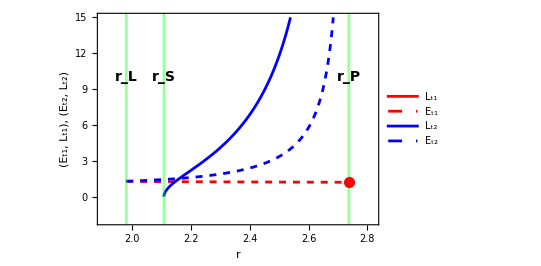

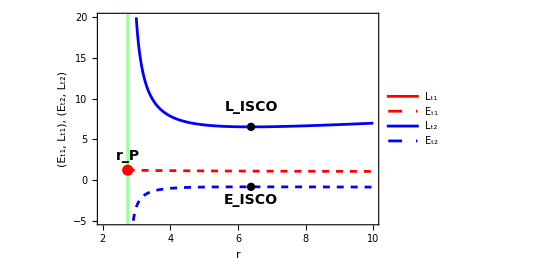

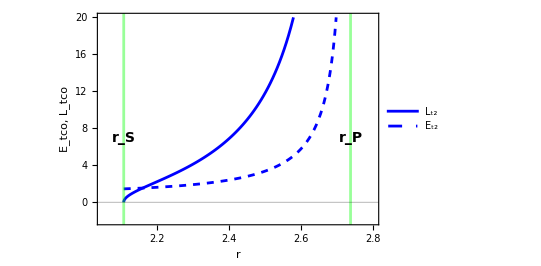

```mathematica
ClearAll["Global`*"]
M=1;Q=0.6;q=3.8;
(*{Ris1,Eis1,Lis1}={};*)
{Ris2,Eis2,Lis2}={6.384943395371074,-0.8363965514840145,6.535644353044245};
f[r]=1-(2M)/r+Q^2/r^2;
f'[r]=D[f[r],r];
SetDirectory[NotebookDirectory[]];
{Et1,Lt1,Et2,Lt2} =ToExpression[Import["expression/EtLt.txt"]];
rh=M+√(M^2-Q^2);rP=1/2(3M+√(9 M^2-8 Q^2));
rL=(3M)/2+1/2 √(9 M^2-8 Q^2-q^2 Q^2);rS=Q^2/(q^2 Q^2-M^2)(M (q^2-1)+√(q^2(q^2-1)(M^2-Q^2)));
{"rh"->rh,"rL"->rL,"rs"->rS,"rp"->rP}
{Je2,Jl2}={Et1,Lt1}/.r->rP-10^-4
(* remark: Jl2 is a imaginary *)
ran1={1.9,2.82};ran2={-2,15};

fig1=Plot[{Lt1,Et1,Lt2,Et2},{r,rL,rP-10^-4},PlotRange->{ran1,ran2},PlotPoints->100,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["(E_t1, L_t1),  (E_t2, L_t2)",18,Italic]},AspectRatio->2/3,PlotLegends->Placed[LineLegend[{Style["L_t1",14],Style["E_t1",14],Style["L_t2",14],Style["E_t2",14]},LegendLayout->{"Column",1}],{0.4,0.75}],GridLines->{{{rL,Directive[Green,Thickness[0.005]] },{rP,Directive[Green,Thickness[0.005]]},{rS,Directive[Green,Thickness[0.005]]}}, {}},Epilog->{Text[Style["r_L",14,Black,Bold],{rL,10}],Text[Style["r_P",14,Black,Bold],{rP,10}],Text[Style["r_S",14,Black,Bold],{rS,10}],Red,Thick,PointSize[0.02],Point[{rP,Je2}](*,Point[{rP,Jl2}]*)(*,Circle[{rP,Je2},{0.0001,4}]*)}]


(* Here we need the zoom in figure for the interveal [rL,rP]. *)
ran1={2,10};ran2={-5,20};
fig2=Plot[{Lt1,Et1,Lt2,Et2},{r,rP,10},PlotRange->{ran1,ran2},PlotPoints->100,PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed}},Frame->True,LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["(E_t1, L_t1),  (E_t2, L_t2)",18,Italic]},AspectRatio->2/3,GridLines->{{ {rP,Directive[Green,Thickness[0.005]]} (*,{rS,Directive[Green,Thickness[0.005]]}*) }, {}},
PlotLegends->Placed[LineLegend[{Style["L_t1",14],Style["E_t1",14],Style["L_t2",14],Style["E_t2",14]},LegendLayout->{"Column",1}],{0.85,0.75}],Epilog->{  Text[Style["r_P",14,Black,Bold],{rP,3}](*,Text[Style["r_S",14,Black,Bold],{rS,3}]*) ,Red,Thick,PointSize[0.02],Point[{rP,Je2}](*,Point[{rP,Jl2}]*),Text[Style["L_ISCO",14,Black,Bold],{Ris2,9}],Text[Style["E_ISCO",14,Black,Bold],{Ris2,-2.5}],Black,PointSize[0.015],(*Point[{Ris1,Eis1}],Point[{Ris1,Lis1}],*) Point[{Ris2,Eis2}],Point[{Ris2,Lis2}]}]

(* Here we focus on positive energy part. *)
(* completed TCO *)
figb=Plot[{Et2,Lt2},{r,rS,rP},PlotRange->{{2.05,2.8},{-2,20}},Frame->True,PlotPoints->100,PlotStyle->{{Blue,Dashed},Blue},LabelStyle->Directive[Bold, Black],FrameTicksStyle->12,FrameLabel->{Style["r",18,Italic],Style["E_tco, L_tco",18,Italic]},AspectRatio->2/3,GridLines->{{{rP,Directive[Green,Thickness[0.005]]},{rS,Directive[Green,Thickness[0.005]]}}, {{0,Directive[Black]}}},PlotLegends->Placed[LineLegend[{Style["E_t2",14],Style["L_t2",14]},LegendLayout->{"ReversedRow",2}],{0.35,0.7}],Epilog->{Text[Style["r_P",14,Black,Bold],{rP,7}],Text[Style["r_S",14,Black,Bold],{rS,7}]}
]
```